```mathematica
Exit[]
```

```mathematica
SN[x_]:= CDF[NormalDistribution[],x];
d[sk_,s_,r_,T_]:=(Log[sk]+(r+s^2/2)T)/s/Sqrt[T];
BS[s_,SK_,r_,T_]:=SK  SN[d[SK,s,r,T]]-Exp[-r T]SN[d[SK,s,r,T]-s Sqrt[T]];d[sk_,s_,r_,T_]:=(Log[sk]+(r+s^2/2)T)/s/Sqrt[T];
d2[s_,x_,T_]:=(-Log[1+Abs[x]]+s^2/2 T)/s/Sqrt[T];
ANDR[x_,s_,T_]:=Max[x,0]+SN[d2[s,x,T]]-(1+Abs[x])SN[d2[s,x,T]-s Sqrt[T]]+s^2/4 NIntegrate[SN[d2[s,x,T-t]],{t,0,T}];

Preis1[Startkapital_, Gewinnschwelle_,Sigma_, Laufzeit_,Zins_]:=Gewinnschwelle*BS[Sigma,Startkapital/Gewinnschwelle,Zins,Laufzeit];
Hedge1[Startkapital_, Gewinnschwelle_,Sigma_, Laufzeit_,Zins_]:= Gewinnschwelle D[BS[Sigma,sta/Gewinnschwelle,Zins,Laufzeit],sta]/.sta->Startkapital;

Preis2[Aktienkurs__,Portfoliowert_,Sigma_,Laufzeit_]:=N[ Aktienkurs ANDR[Portfoliowert/Aktienkurs,Sigma,Laufzeit]];

Hedge2[q_,Aktienkurs_,Portfoliowert_,Sigma_,Laufzeit_]:=Aktienkurs(
(Preis2[Aktienkurs+0.0001,Portfoliowert,Sigma,Laufzeit]-Preis2[Aktienkurs-0.0001,Portfoliowert,Sigma,Laufzeit])/0.0002+q (Preis2[Aktienkurs,Portfoliowert+0.0001,Sigma,Laufzeit]-Preis2[Aktienkurs,Portfoliowert-0.0001,Sigma,Laufzeit])/0.0002)
```

```mathematica
P=10;M=10;σ=0.5;r=0.08;T=1/12;
Preis1[P,M,σ,T,r]
 Hedge1[P*0.7,M,σ,T,r]
```

0.607246

0.00931734

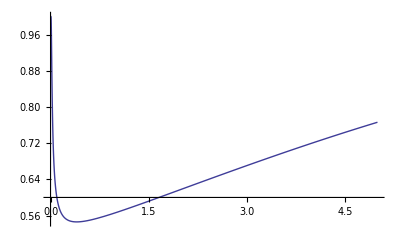

```mathematica
Plot[Hedge1[P,M,σ1,T,r],{σ1,0.00001,5},PlotRange->All]
```

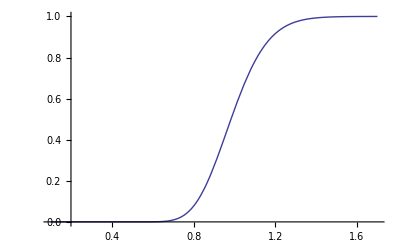

```mathematica
Plot[Hedge1[σ1 M,M,σ,T,r],{σ1,0.1,1.7},PlotRange->All]
```

```mathematica
Log[1+0.045]
```

0.0440169

```mathematica
Preis2[100,0,0.3,0.25]
Hedge2[-1,100,0,0.3,0.25]
```

6.27099

-43.729